# Ecuaciones diferenciales: Método de Euler

```mathematica
sol = y[x]/.DSolve[{y'[x]==x^2-y[x]^2,y[1]==1},y[x],x]
```

{-((-ⅈ x^2 BesselJ[-5/4,(ⅈ x^2)/2] BesselJ[-3/4,ⅈ/2]+ⅈ x^2 BesselJ[-5/4,ⅈ/2] BesselJ[-3/4,(ⅈ x^2)/2]-x^2 BesselJ[-3/4,(ⅈ x^2)/2] BesselJ[-1/4,ⅈ/2]-BesselJ[-3/4,ⅈ/2] BesselJ[-1/4,(ⅈ x^2)/2]+x^2 BesselJ[-5/4,(ⅈ x^2)/2] BesselJ[1/4,ⅈ/2]-ⅈ BesselJ[-1/4,(ⅈ x^2)/2] BesselJ[1/4,ⅈ/2]-ⅈ x^2 BesselJ[-3/4,(ⅈ x^2)/2] BesselJ[3/4,ⅈ/2]+ⅈ x^2 BesselJ[-3/4,ⅈ/2] BesselJ[3/4,(ⅈ x^2)/2]-x^2 BesselJ[1/4,ⅈ/2] BesselJ[3/4,(ⅈ x^2)/2])/(x (2 BesselJ[-3/4,ⅈ/2] BesselJ[-1/4,(ⅈ x^2)/2]+2 ⅈ BesselJ[-1/4,(ⅈ x^2)/2] BesselJ[1/4,ⅈ/2]-BesselJ[-5/4,ⅈ/2] BesselJ[1/4,(ⅈ x^2)/2]-ⅈ BesselJ[-1/4,ⅈ/2] BesselJ[1/4,(ⅈ x^2)/2]+BesselJ[1/4,(ⅈ x^2)/2] BesselJ[3/4,ⅈ/2])))}

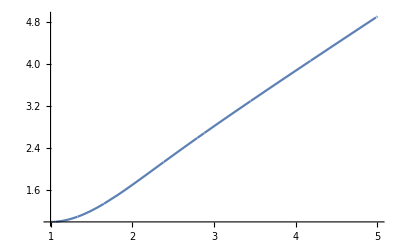

```mathematica
Plot[sol,{x,1,5}]
```

## Representación gráfica para el punto x_0= 1, y(x_0) = 1

```mathematica
f[x_,y_]=x^2-y^2;
```

```mathematica
xn = 1;
yn = 1;
h = 0.3;
results = {{xn,yn}};

Do[
xnp = xn + h;
ynp= yn + h f[xn,yn];
xn = xnp;
yn = ynp;
AppendTo[results,{xn,yn}];
,10
]
```

```mathematica
results
```

{{1,1},{1.3,1.},{1.6,1.207},{1.9,1.53795},{2.2,1.91136},{2.5,2.26737},{2.8,2.60008},{3.1,2.92396},{3.4,3.2421},{3.7,3.55674},{4.,3.86863}}

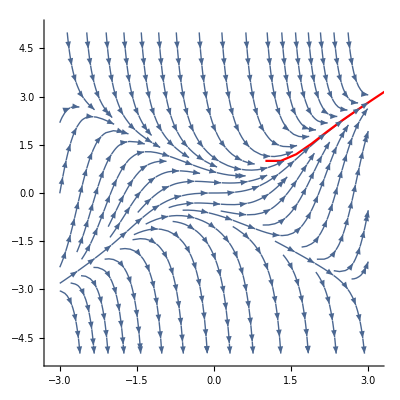

```mathematica
Show[
StreamPlot[{1,f[x,y]},{x,-3,3},{y,-5,5},Frame->False,Axes->True],
ListLinePlot[results,PlotStyle->{Red}]
]
```

## Representación gráfica interactiva

```mathematica
MetodoEuler[{x0_,y0_},h_,n_]:=Block[{xn,yn,results,xnp,ynp},
xn = x0;
yn = y0;
results = {{xn,yn}};

Do[
xnp = xn + h;
ynp= yn + h f[xn,yn];
xn = xnp;
yn = ynp;
AppendTo[results,{xn,yn}];
,n
];

results
];
```

```mathematica
Manipulate[
Show[
StreamPlot[
{1,f[x,y]},{x,-3,3},{y,-5,5},
PlotRange->{{-3,3},{-5,5}},
Frame->True,
ImageSize->450,
BaseStyle->FontSize->13,
FrameLabel->{Style["x",15], Style["y",15]},
PlotTheme->"Monochrome",
GridLines->Automatic
],
ListLinePlot[MetodoEuler[p,h,20],PlotStyle->{Red},PlotRange->{{-3,3},{-5,5}}]
],
{{p,{1,1}},Locator},{{h,0.1},0.0001,1},
SaveDefinitions->True
]
```

## Ejemplo: Péndulo simple

La dinámica del péndulo simple está descrita por la ecuación diferencial

θ^(..)(t)+ g/l Sin(θ(t)) = 0

-Graphics-

Para trabajar este sistema es común realizar una aproximación para ángulos pequeños, argumentando que θ ≃ Sin(θ) se suele reescribir como

θ^(..)(t)+ g/l θ(t) = 0.

La ventaja de expresarlo de esta manera es que la ecuación posee soluciones analíticas, las cuales en Mathematica podemos obtener utilizando DSolve.

```mathematica
DSolve[θ''[t]+g/l θ[t]==0,θ,t]
```

{{θ→Function[{t},C[1] Cos[(√g t)/(√l)]+C[2] Sin[(√g t)/(√l)]]}}

DSolve siempre nos devuelve la forma más general de una solución, incluyendo constantes arbitrarias denotadas por C[n]. Estas pueden ser  eliminadas introduciendo constricciones al sistema de ecuaciones diferenciales.

```mathematica
DSolve[{θ''[t]+g/l θ[t]==0,θ[0]==1,θ'[0]==0},θ,t]
```

{{θ→Function[{t},Cos[(√g t)/(√l)]]}}

Una vez resuelta la ecuación diferencial, ¿cómo se grafica? La solución viene expresada como una regla de sustitución, de manera que aplican las mismas reglas que cuando resolvimos ecuaciones algebraicas.

{{θ→Function[{t},1. Cos[3.1305 t]]}}

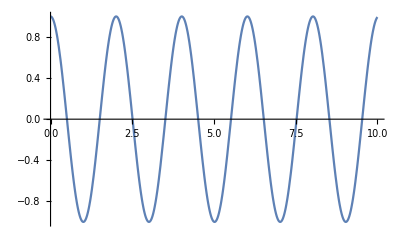

```mathematica
solucion = With[{g=9.8,l=1},DSolve[{θ''[t]+g/l θ[t]==0,θ[0]==1,θ'[0]==0},θ,t]]
Plot[θ[t]/.First[solucion],{t,0,10}]
```

Si intentamos hacer lo mismo con la ecuación diferencial sin la aproximación DSolve devuelve errores. La causa de esto es que no existe una solución analítica.

```mathematica
DSolve[{θ''[t]+g/l Sin[θ[t]]==0,θ[0]==1,θ'[0]==0},θ,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

DSolve::bvfail: For some branches of the general solution, unable to solve the conditions.

En estos casos conviene resolver la ecuación numéricamente:

```mathematica
tn = 0;
θn = 1;
θpn = 0;
θppn = 0;
g=9.8;
l=1;

h = 0.005;
results = {{tn,θn}};

Do[
tn = tn+h;
nθn = θn + h θpn;
nθpn= θpn- h g/l Sin[θn];
θn = nθn;
θpn = nθpn;

AppendTo[results,{tn,θn}];
,2000
]
```

```mathematica
results[[-1]]
```

{10.,-1.06317}

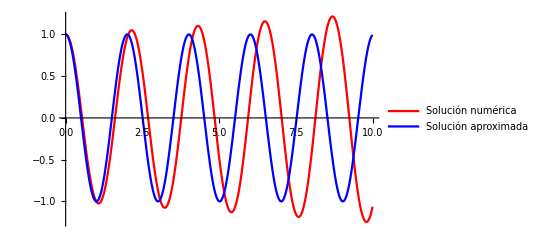

```mathematica
Show[
ListLinePlot[results,PlotStyle->Red,PlotLegends->{"Solución numérica"}],
Plot[θ[t]/.First[solucion],{t,0,10},PlotStyle->Blue,PlotLegends->{"Solución aproximada"}]
]
```

La solución numérica según Mathematica es:

```mathematica
completa = With[{g=9.8,l = 1},NDSolve[{θ''[t]+g/l Sin[θ[t]]==0,θ[0]==1,θ'[0]==0},θ,{t,0,10}]]
```

{{θ→InterpolatingFunction[…]}}

```mathematica
aproximacion = With[{g=9.8,l = 1},NDSolve[{θ''[t]+g/l θ[t]==0,θ[0]==1,θ'[0]==0},θ,{t,0,10}]]
```

{{θ→InterpolatingFunction[…]}}

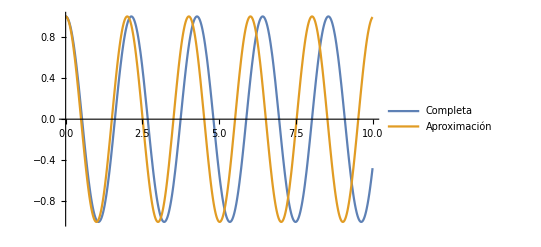

```mathematica
Plot[Evaluate[θ[t]/.{First[completa],First[aproximacion]}], {t,0,10},PlotLegends->{"Completa","Aproximación"}]
```